## Question 1

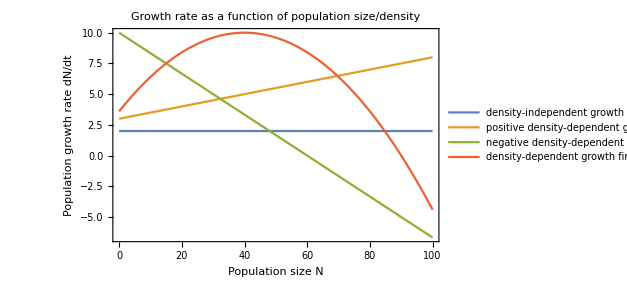

```mathematica
Plot[{2,1/20*x+3,10-1/6 x,-0.004(x-40)^2+10},{x,0,100},Frame->True,FrameLabel->{"Population size N","Population growth rate dN/dt"},PlotLabel->Style["Growth rate as a function of population size/density",18],PlotLegends->{"density-independent growth","positive density-dependent growth","negative density-dependent growth","density-dependent growth \nfirst positive, then negative"}]
```

```mathematica
logisticGrowthRate[n_,r_,k_]:=r*n(1-n/k)
```

```mathematica
alleeEffectGrowthRate[n_,u_,c_,v_]:=((u*n)/(v+n)-c*n)n
```

## Question 2

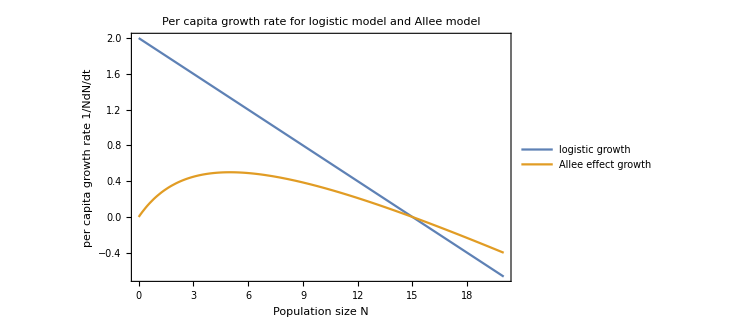

```mathematica
Plot[{1/n*logisticGrowthRate[n,2,15],1/n *alleeEffectGrowthRate[n,2,0.1,5]},{n,0,20},Frame->True,FrameLabel->{Style["Population size N",15],Style["per capita growth rate 1/NdN/dt",15]},PlotLabel->Style["Per capita growth rate for logistic model and Allee model",20],PlotLegends->{"logistic growth", "Allee effect growth"}]
```

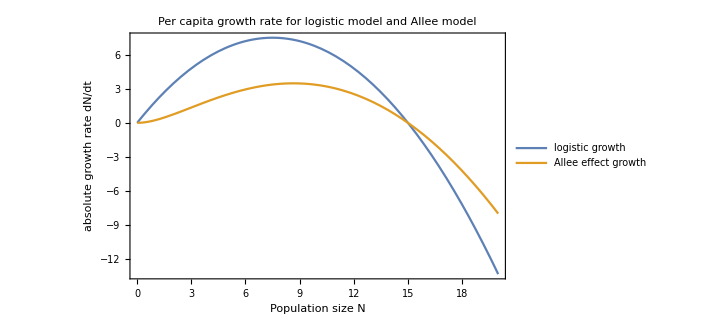

```mathematica
Plot[{logisticGrowthRate[n,2,15],alleeEffectGrowthRate[n,2,0.1,5]},{n,0,20},Frame->True,FrameLabel->{Style["Population size N",15],Style["absolute growth rate dN/dt",15]},PlotLabel->Style["Per capita growth rate for logistic model and Allee model",20],PlotLegends->{"logistic growth", "Allee effect growth"}]
```

Finding

```mathematica
Solve[D[logisticGrowthRate[n,2,15],n]==0]
```

{{n→15/2}}

```mathematica
logisticGrowthRate[7.5,2,15]//N
```

7.5

```mathematica
Solve[D[alleeEffectGrowthRate[n,2,0.1,5],n]==0&&n>0,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→8.66025}}

```mathematica
alleeEffectGrowthRate[8.66025,2,0.1,5]
```

3.48076

```mathematica
Solve[D[1/n*alleeEffectGrowthRate[n,2,0.1,5],n]==0&&n>0,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→5.}}

```mathematica
1/5*alleeEffectGrowthRate[5,2,0.1,5]
```

0.5

## Question 3